## Stability Region Code

```mathematica
getRegion[A_,B_] := 
	Module[{a,b,c,d,r},
		{a,b} = Assuming[θ∈Reals,ReIm[∑_(m=0)^(Length[A]-1) A[[m+1]] ⅇ^(m ⅈ θ)]//FullSimplify];
		{c,d} = Assuming[θ∈Reals,ReIm[∑_(m=0)^(Length[B]-1) B[[m+1]] ⅇ^(m ⅈ θ)]//FullSimplify];
		r[θ_] = {(a c+b d)/(c^2+d^2),(b c-a d)/(c^2+d^2)}//FullSimplify
	]
getPlot[A_,B_] := 
	Module[{r},
		r[θ_] = getRegion[A,B];
		ParametricPlot[r[θ],{θ,0,2π}]
	]
```

## Orders of Convergence Code

```mathematica
ord=6;(* Order to expand to *)
Y[t_]=Series[y[t],{t,tn,ord-1}]//Normal;
yn[n_Integer,p_Integer]:=Derivative[p][Y][tn+n h]+O[h]^ord
getOrd[A_,B_]:=∑_(s=0)^(Length[A]-1) A[[s+1]]yn[s,0]-h∑_(s=0)^(Length[B]-1) B[[s+1]]yn[s,1];
```

## (1)

### (a) Adams-Bashforth with s = 2

{(8 Sin[θ/2]^4)/(-5+3 Cos[θ]),(2 (-2+Cos[θ]) Sin[θ])/(-5+3 Cos[θ])}

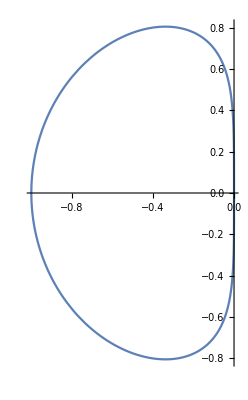

5/12 y^(3)[tn] h^3+3/8 y^(4)[tn] h^4+47/240 y^(5)[tn] h^5+O[h]^6

```mathematica
getRegion[{0,-1,1},{-1/2,3/2,0}]
getPlot[{0,-1,1},{-1/2,3/2,0}]
getOrd[{0,-1,1},{-1/2,3/2,0}]
```

### (b) Adams-Bashforth with s = 3

{(6 ((5-16 Cos[θ]+23 Cos[2 θ]) Re[ⅇ^(2 ⅈ θ) (-1+ⅇ^(ⅈ θ))]+2 (-8+23 Cos[θ]) Im[ⅇ^(2 ⅈ θ) (-1+ⅇ^(ⅈ θ))] Sin[θ]))/(405-448 Cos[θ]+115 Cos[2 θ]),(6 ((5-16 Cos[θ]+23 Cos[2 θ]) Im[ⅇ^(2 ⅈ θ) (-1+ⅇ^(ⅈ θ))]+2 (-8+23 Cos[θ]) Re[ⅇ^(2 ⅈ θ)-ⅇ^(3 ⅈ θ)] Sin[θ]))/(405-448 Cos[θ]+115 Cos[2 θ])}

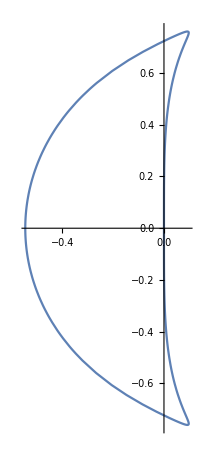

3/8 y^(4)[tn] h^4+193/360 y^(5)[tn] h^5+O[h]^6

```mathematica
getRegion[{0,0,-1,1},{5/12,-4/3,23/12,0}]
getPlot[{0,0,-1,1},{5/12,-4/3,23/12,0}]
getOrd[{0,0,-1,1},{5/12,-4/3,23/12,0}]
```

### (c) Adams-Moulton with s = 2

{(48 Sin[θ/2]^4)/(-32 Cos[θ]+5 (-9+Cos[2 θ])),(6 (-14 Sin[θ]+Sin[2 θ]))/(-32 Cos[θ]+5 (-9+Cos[2 θ]))}

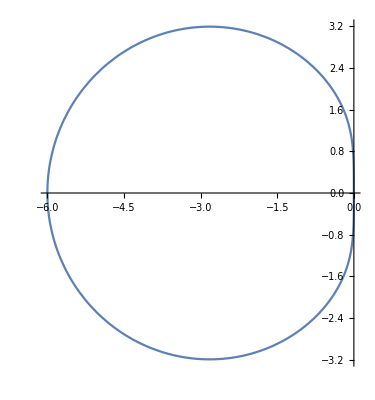

-1/24 y^(4)[tn] h^4-17/360 y^(5)[tn] h^5+O[h]^6

```mathematica
getRegion[{0,-1,1},{-1/12,2/3,5/12}]
getPlot[{0,-1,1},{-1/12,2/3,5/12}]
getOrd[{0,-1,1},{-1/12,2/3,5/12}]
```

## (2)

### (a) BDF of order s = 2

{4 Sin[θ/2]^4,-((-2+Cos[θ]) Sin[θ])}

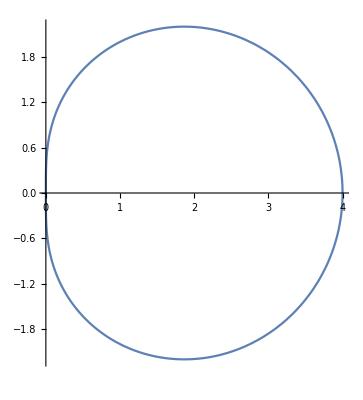

-2/9 y^(3)[tn] h^3-5/18 y^(4)[tn] h^4+O[h]^5

```mathematica
getRegion[{1/3,-4/3,1},{0,0,2/3}]
getPlot[{1/3,-4/3,1},{0,0,2/3}]
getOrd[{1/3,-4/3,1},{0,0,2/3}]
```

### (b) BDF of order s = 3

{4/3 (1-4 Cos[θ]) Sin[θ/2]^4,1/3 (-9 (-1+Cos[θ]) Sin[θ]+Sin[3 θ])}

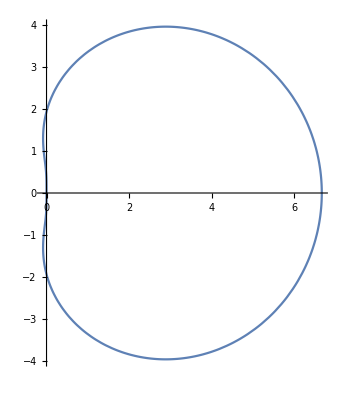

-3/22 y^(4)[tn] h^4+O[h]^5

```mathematica
getRegion[{-2/11,9/11,-18/11,1},{0,0,0,6/11}]
getPlot[{-2/11,9/11,-18/11,1},{0,0,0,6/11}]
getOrd[{-2/11,9/11,-18/11,1},{0,0,0,6/11}]
```

## My own stuff

### 4-step Adams-Bashforth

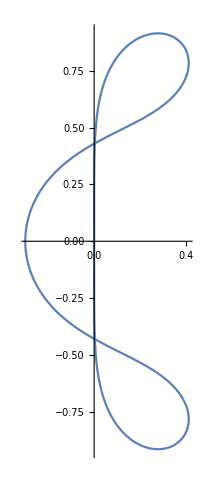

251/720 y^(5)[tn] h^5+O[h]^6

```mathematica
getPlot[{0,0,0,-1,1},1/24{-9,37,-59,55}]
getOrd[{0,0,0,-1,1},1/24{-9,37,-59,55}]
```